```mathematica
ClearAll["Global`*"]
```

```mathematica
wd=SetDirectory@NotebookDirectory[];


e0=Take[Import[wd<>"/../../output/e_0.250.dat"]][[All,{1,2,4}]];
e1=Take[Import[wd<>"/../../output/e_0.750.dat"]][[All,{1,2,4}]];
e2=Take[Import[wd<>"/../../output/e_1.250.dat"]][[All,{1,2,4}]];
e3=Take[Import[wd<>"/../../output/e_1.750.dat"]][[All,{1,2,4}]];
e4=Take[Import[wd<>"/../../output/e_2.250.dat"]][[All,{1,2,4}]];
e5=Take[Import[wd<>"/../../output/e_2.750.dat"]][[All,{1,2,4}]];
e6=Take[Import[wd<>"/../../output/e_3.250.dat"]][[All,{1,2,4}]];

plpt0=Take[Import[wd<>"/../../output/plpt_0.250.dat"]][[All,{1,2,4}]];
plpt1=Take[Import[wd<>"/../../output/plpt_0.750.dat"]][[All,{1,2,4}]];
plpt2=Take[Import[wd<>"/../../output/plpt_1.250.dat"]][[All,{1,2,4}]];
plpt3=Take[Import[wd<>"/../../output/plpt_1.750.dat"]][[All,{1,2,4}]];
plpt4=Take[Import[wd<>"/../../output/plpt_2.250.dat"]][[All,{1,2,4}]];
plpt5=Take[Import[wd<>"/../../output/plpt_2.750.dat"]][[All,{1,2,4}]];
plpt6=Take[Import[wd<>"/../../output/plpt_3.250.dat"]][[All,{1,2,4}]];

ux0=Take[Import[wd<>"/../../output/ux_0.250.dat"]][[All,{1,2,4}]];
ux1=Take[Import[wd<>"/../../output/ux_0.750.dat"]][[All,{1,2,4}]];
ux2=Take[Import[wd<>"/../../output/ux_1.250.dat"]][[All,{1,2,4}]];
ux3=Take[Import[wd<>"/../../output/ux_1.750.dat"]][[All,{1,2,4}]];
ux4=Take[Import[wd<>"/../../output/ux_2.250.dat"]][[All,{1,2,4}]];
ux5=Take[Import[wd<>"/../../output/ux_2.750.dat"]][[All,{1,2,4}]];
ux6=Take[Import[wd<>"/../../output/ux_3.250.dat"]][[All,{1,2,4}]];

ur0=Take[Import[wd<>"/../../output/ur_0.250.dat"]][[All,{1,2,4}]];
ur1=Take[Import[wd<>"/../../output/ur_0.750.dat"]][[All,{1,2,4}]];
ur2=Take[Import[wd<>"/../../output/ur_1.250.dat"]][[All,{1,2,4}]];
ur3=Take[Import[wd<>"/../../output/ur_1.750.dat"]][[All,{1,2,4}]];
ur4=Take[Import[wd<>"/../../output/ur_2.250.dat"]][[All,{1,2,4}]];
ur5=Take[Import[wd<>"/../../output/ur_2.750.dat"]][[All,{1,2,4}]];
ur6=Take[Import[wd<>"/../../output/ur_3.250.dat"]][[All,{1,2,4}]];

aL0=Take[Import[wd<>"/../../output/aL_0.250.dat"]][[All,{1,2,4}]];
aL1=Take[Import[wd<>"/../../output/aL_0.750.dat"]][[All,{1,2,4}]];
aL2=Take[Import[wd<>"/../../output/aL_1.250.dat"]][[All,{1,2,4}]];
aL3=Take[Import[wd<>"/../../output/aL_1.750.dat"]][[All,{1,2,4}]];
aL4=Take[Import[wd<>"/../../output/aL_2.250.dat"]][[All,{1,2,4}]];
aL5=Take[Import[wd<>"/../../output/aL_2.750.dat"]][[All,{1,2,4}]];
aL6=Take[Import[wd<>"/../../output/aL_3.250.dat"]][[All,{1,2,4}]];
```

```mathematica
max=4.0;

dx= 0.05;
xpts=201;
ypts=201;

xmin=-dx*(xpts-1)/2;
xmax=dx*(xpts-1)/2;
(* i+nx*(j+ny*k) *)
s1=1 + xpts * (ypts-1)/2 
s2=s1+xpts-1
```

20101

20301

```mathematica
pts=1/dx;

DarkBlueBlueBlend=Table[Blend[{Darker[Blue],Blue},dx*i],{i,0,pts-1}];
BlueCyanBlend=Table[Blend[{Blue,Cyan},dx*i],{i,0,pts-1}];
CyanGreenBlend=Table[Blend[{Cyan,Green},dx*i],{i,0,pts-1}];
GreenYellowBlend=Table[Blend[{Green,Yellow},dx*i],{i,0,pts-1}];
YellowOrangeBlend=Table[Blend[{Yellow,Orange},dx*i],{i,0,pts-1}];
OrangeRedBlend=Table[Blend[{Orange,Red},dx*i],{i,0,pts-1}];
RedDarkRedBlend=Table[Blend[{Red,Darker[Red]},dx*i],{i,0,pts}];

colors=Flatten[{DarkBlueBlueBlend, BlueCyanBlend, CyanGreenBlend, GreenYellowBlend, YellowOrangeBlend, OrangeRedBlend,RedDarkRedBlend}];

colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Energy"]=Function[x,Blend[Transpose[{colorpts,colors}],x ]];
ColorData["Flow"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

BarLegend[{ColorData["Energy"],{0,1}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
```

```mathematica
(* Gubser solution *)
q=1.0;
κ[τ_,r_]:=ArcTanh[(2.0*q^2*τ*Abs[r])/(1.0+q^2*(τ^2+r^2))];
ux[τ_,r_]:=Sinh[κ[τ,r]]*Sign[r];

gubserPath = wd<>"/gubser_data/5fm";

e0test=Take[Import[gubserPath<>"/e_0.250.dat"]];
e1test=Take[Import[gubserPath<>"/e_0.750.dat"]];
e2test=Take[Import[gubserPath<>"/e_1.250.dat"]];
e3test=Take[Import[gubserPath<>"/e_1.750.dat"]];
e4test=Take[Import[gubserPath<>"/e_2.250.dat"]];
e5test=Take[Import[gubserPath<>"/e_2.750.dat"]];
e6test=Take[Import[gubserPath<>"/e_3.250.dat"]];

plpt0test=Take[Import[gubserPath<>"/plpt_0.250.dat"]];
plpt1test=Take[Import[gubserPath<>"/plpt_0.750.dat"]];
plpt2test=Take[Import[gubserPath<>"/plpt_1.250.dat"]];
plpt3test=Take[Import[gubserPath<>"/plpt_1.750.dat"]];
plpt4test=Take[Import[gubserPath<>"/plpt_2.250.dat"]];
plpt5test=Take[Import[gubserPath<>"/plpt_2.750.dat"]];
plpt6test=Take[Import[gubserPath<>"/plpt_3.250.dat"]];

aL0test=Take[Import[gubserPath<>"/aL_0.250.dat"]];
aL1test=Take[Import[gubserPath<>"/aL_0.750.dat"]];
aL2test=Take[Import[gubserPath<>"/aL_1.250.dat"]];
aL3test=Take[Import[gubserPath<>"/aL_1.750.dat"]];
aL4test=Take[Import[gubserPath<>"/aL_2.250.dat"]];
aL5test=Take[Import[gubserPath<>"/aL_2.750.dat"]];
aL6test=Take[Import[gubserPath<>"/aL_3.250.dat"]];

ux0test=Table[{xmin+i*dx,ux[0.25,xmin+i*dx]},{i,0,xpts-1}];
ux1test=Table[{xmin +i*dx,ux[0.75,xmin+i*dx]},{i,0,xpts-1}];
ux2test=Table[{xmin +i*dx,ux[1.25,xmin+i*dx]},{i,0,xpts-1}];
ux3test=Table[{xmin +i*dx,ux[1.75,xmin+i*dx]},{i,0,xpts-1}];
ux4test=Table[{xmin +i*dx,ux[2.25,xmin+i*dx]},{i,0,xpts-1}];
ux5test=Table[{xmin +i*dx,ux[2.75,xmin+i*dx]},{i,0,xpts-1}];
ux6test=Table[{xmin +i*dx,ux[3.25,xmin+i*dx]},{i,0,xpts-1}];

(*****************************************)

e0slice=e0[[s1;;s2,{1,3}]];
e1slice=e1[[s1;;s2,{1,3}]];
e2slice=e2[[s1;;s2,{1,3}]];
e3slice=e3[[s1;;s2,{1,3}]];
e4slice=e4[[s1;;s2,{1,3}]];
e5slice=e5[[s1;;s2,{1,3}]];
e6slice=e6[[s1;;s2,{1,3}]];

plpt0slice=plpt0[[s1;;s2,{1,3}]];
plpt1slice=plpt1[[s1;;s2,{1,3}]];
plpt2slice=plpt2[[s1;;s2,{1,3}]];
plpt3slice=plpt3[[s1;;s2,{1,3}]];
plpt4slice=plpt4[[s1;;s2,{1,3}]];
plpt5slice=plpt5[[s1;;s2,{1,3}]];
plpt6slice=plpt6[[s1;;s2,{1,3}]];

ux0slice=ux0[[s1;;s2,{1,3}]];
ux1slice=ux1[[s1;;s2,{1,3}]];
ux2slice=ux2[[s1;;s2,{1,3}]];
ux3slice=ux3[[s1;;s2,{1,3}]];
ux4slice=ux4[[s1;;s2,{1,3}]];
ux5slice=ux5[[s1;;s2,{1,3}]];
ux6slice=ux6[[s1;;s2,{1,3}]];

aL0slice=aL0[[s1;;s2,{1,3}]];
aL1slice=aL1[[s1;;s2,{1,3}]];
aL2slice=aL2[[s1;;s2,{1,3}]];
aL3slice=aL3[[s1;;s2,{1,3}]];
aL4slice=aL4[[s1;;s2,{1,3}]];
aL5slice=aL5[[s1;;s2,{1,3}]];
aL6slice=aL6[[s1;;s2,{1,3}]];


magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[2],Opacity[0.3]};
redTran={Red,AbsoluteThickness[2],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[2],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
purpleTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[2],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
red={Red,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
blue={Blue,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
purple={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]};

style={magentaTran,redTran,orangeTran,greenTran,cyanTran,blueTran,purpleTran,magenta,red,orange,green,cyan, blue,purple};
```

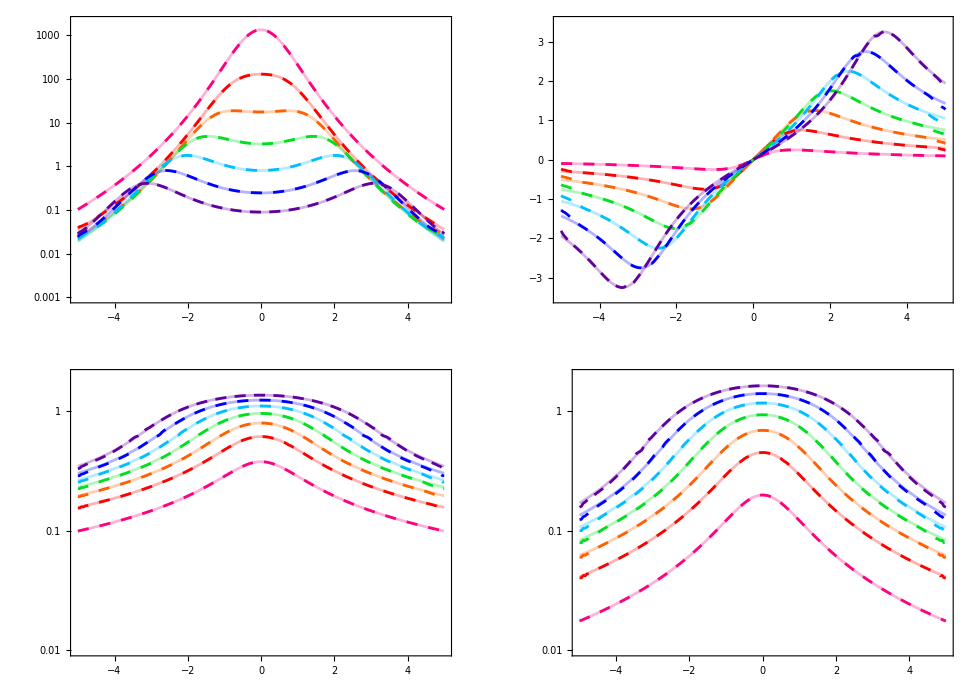

```mathematica
GraphicsGrid[{{
ListLogPlot[{e0test,e1test,e2test,e3test,e4test,e5test,e6test,e0slice,e1slice,e2slice,e3slice,e4slice,e5slice,e6slice},Joined->True,InterpolationOrder->1,PlotRange->{{xmin,xmax},{0.001,2000}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListPlot[{ux0test,ux1test,ux2test,ux3test,ux4test,ux5test,ux6test,ux0slice,ux1slice,ux2slice,ux3slice,ux4slice,ux5slice,ux6slice},Joined->True,InterpolationOrder->1,PlotRange->{{xmin,xmax},{-3.5,3.5}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]},

{ListLogPlot[{aL0test,aL1test,aL2test,aL3test,aL4test,aL5test,aL6test,aL0slice,aL1slice,aL2slice,aL3slice,aL4slice,aL5slice,aL6slice},Joined->True,InterpolationOrder->1,PlotRange->{{xmin,xmax},{0.01,2}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListLogPlot[{plpt0test,plpt1test,plpt2test,plpt3test,plpt4test,plpt5test,plpt6test,plpt0slice,plpt1slice,plpt2slice,plpt3slice,plpt4slice,plpt5slice,plpt6slice},Joined->True,InterpolationOrder->1,PlotRange->{{xmin,xmax},{0.01,2.0}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]}}]

Export[wd<>"/gubser_aniso_test.pdf",%];
```

```mathematica
(* PL Matching *)
```

```mathematica
Max[e0[[All,3]]]
Max[e2[[All,3]]]
Max[e4[[All,3]]]
Max[e6[[All,3]]]
```

1335.73

18.626

1.80101

0.448613

```mathematica
plot=Grid[{{ListDensityPlot[e0,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e0[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e2,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e2[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e4,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e4[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e6,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e6[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250]},

{ListDensityPlot[ur0,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur2,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur4,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur6,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250]}}];
```

```mathematica
Export[wd<>"/gubser_aniso_2d.eps",plot];
```

```mathematica
Max[e6[[All,3]]]
```

0.475641

```mathematica
ListDensityPlot[e6,PlotRange->{{-5,5},{-5,5},{0,Max[e6[[All,3]]]}},PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e6[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->500]
```

-Graphics-

```mathematica
Max[e6[[All,3]]]
e6slice=e6[[s1;;s2,{1,3}]];
Max[e6slice[[All,2]]]
Max[e6test[[All,2]]]
```

0.45999

0.409114

0.407332

```mathematica
e6expect=0.40828933;

e6maxNewKT=0.47564077;

e6maxPartialKT=0.44861276;

KTplot=Grid[{{ListContourPlot[e6,PlotRange->{{-5,5},{-5,5},{0,e6maxPartialKT}},Contours->15,ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->500],

ListContourPlot[ur6,PlotRange->{{-5,5},{-5,5},{0,4}},Contours->15,ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->500]}}]

Export[wd<>"/gubser_2d_old_KT.png",KTplot];
```

0.408289

-Graphics-